```mathematica
alanineFull = Import[NotebookDirectory[]<>"../code/AD_initial_frame.pdb",  "Molecule"];
```

```mathematica
alanine = Import[NotebookDirectory[]<>"../code/AD_initial_frame.pdb"]
alanine = Import[NotebookDirectory[]<>"../code/output.pdb"]
```

-Graphics3D-

-Graphics3D-

```mathematica
alanineMolecule = ConnectedMoleculeComponents[alanineFull][[1]]
```

Molecule[…]

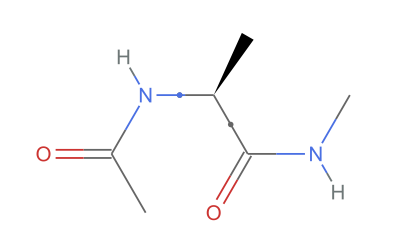

```mathematica
MoleculePlot[alanineMolecule, BondLabels->{Bond[{7, 9}]->MaTeX["\phi", FontSize->28], Bond[{9, 15}]->MaTeX["\psi", FontSize->28 ]},BondLabelStyle->Directive[FontSize->20, Purple],  PlotTheme->"Aromatic"]
```

```mathematica
MoleculeRecognize[%]
```

Molecule[…]

```mathematica
<<MaTeX`
```

```mathematica
torsionAnglesPhi = {5, 7, 9, 11};
torsionAnglesPsi = {11, 9, 15, 16};

scan = Table[
Table[
alanineMolecule = MoleculeModify[alanineMolecule, {"SetTorsionAngle", torsionAnglesPhi->phi}];
alanineMolecule = MoleculeModify[alanineMolecule, {"SetTorsionAngle", torsionAnglesPsi->psi}];
{phi, psi, First@MoleculeValue[alanineMolecule, "MMFFsEnergy"]}
,
{phi, -180, 180, 6}
], {psi, -180, 180,6}];
```

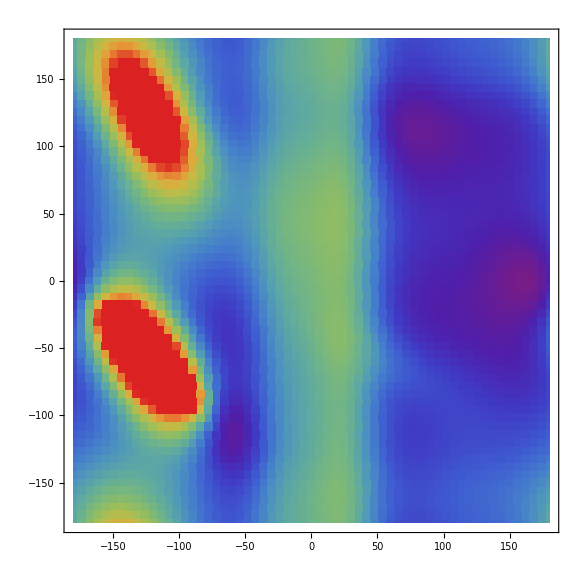

```mathematica
ListDensityPlot[Flatten[scan, 1], ColorFunction->"Rainbow", InterpolationOrder->0, ClippingStyle->Automatic]
```

```mathematica
scan
```

WolframAlphaQueryNoResults*